Alexandria Taylor, 4/10/2019

```mathematica
ClearAll["Global`*"]
```

```mathematica
Question 1)
```

```mathematica
energySol = Solve[(√2 √eVals √m a)/ℏ+ n π==0, eVals]//Flatten
```

{eVals→(n^2 π^2 ℏ^2)/(2 a^2 m)}

```mathematica
energyLevels[n_] = eVals /. energySol
```

(n^2 π^2 ℏ^2)/(2 a^2 m)

```mathematica
(n^2 π^2 ℏ^2)/(2 a^2 m)
```

(n^2 π^2 ℏ^2)/(2 a^2 m)

```mathematica
Elev=energyLevels[n+1] -energyLevels[n]
```

-(n^2 π^2 ℏ^2)/(2 a^2 m)+((1+n)^2 π^2 ℏ^2)/(2 a^2 m)

```mathematica
-(n^2 π^2 ℏ^2)/(2 a^2 m)+((1+n)^2 π^2 ℏ^2)/(2 a^2 m)
```

-(n^2 π^2 ℏ^2)/(2 a^2 m)+((1+n)^2 π^2 ℏ^2)/(2 a^2 m)

```mathematica
Plot[energyLevels[1+1,a]-energyLevels[1,a]/.ruleH,{a, 1 10^-10, 1 10^-9}, PlotRange->Full]
```

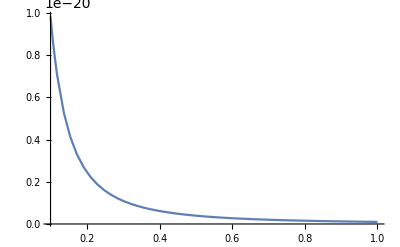

```mathematica
Solve[(6.022 10^23) (energyLevels[1+1]-energyLevels[1])==1,a]/.ruleH
```

{{a→-7.69916×10^-9},{a→7.69916×10^-9}}

```mathematica
Question 2)
```

```mathematica
(* Visually pleasing scaling factor for ψ *)
scaleWF=5 10^-4;
(* Energy levels in chemist-friendly J/mol *)
nAvog = AvogadroConstant * Mole;
ruleH = { m -> ProtonMass * (1/Kilogram) , ℏ -> 1/(2 π) (PlanckConstant /. Joule -> (Kilogram  Meter^2)/Second^2)*(Second/(Kilogram  Meter^2))};
ruleD =  { m -> DeuteronMass* (1/Kilogram), ℏ -> 1/(2 π) (PlanckConstant /. Joule -> (Kilogram  Meter^2)/Second^2)*(Second/(Kilogram  Meter^2))};
```

```mathematica
energyLevels[1+1] -energyLevels[1]
```

```mathematica
(3 π^2 ℏ^2)/(2 a^2 m)/.a->{3.0,5.4,7.7,10.0,12.3}
```

```mathematica
{(1.6449340668482262 ℏ^2)/m,(0.5076956996445142 ℏ^2)/m,(0.24969483220836627 ℏ^2)/m,(0.14804406601634038 ℏ^2)/m,(0.09785449535087604 ℏ^2)/m}/.ruleH
```

```mathematica
{1.0937119332972879*^-41,3.375654115115086*^-42,1.6602137628058006*^-42,9.843407399675593*^-43,6.50631727125097*^-43}×c×s
```

```mathematica
ClearAll[λcal,λobs]
```

```mathematica
λcal={328,101,498,295,195}

λob={163,216,252,282,312}
```

{328,101,498,295,195}

{163,216,252,282,312}

```mathematica
{165,-115,246,13,-117}
```

{165,-115,246,13,-117}

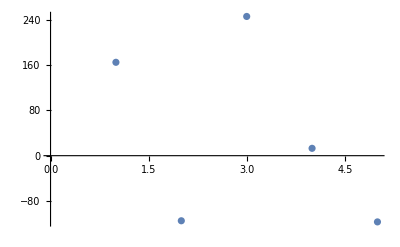

```mathematica
ListPlot[{165,-115,246,13,-117}]
```

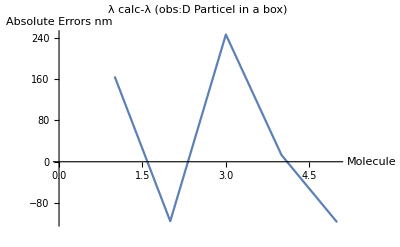

```mathematica
Show[%617,AxesLabel->{HoldForm[Molecule],HoldForm[Absolute Errors nm]},PlotLabel->HoldForm[λ calc-λ (obs:D Particel in a box)],LabelStyle->{GrayLevel[0]}]
```